# Analytic forms with conversion from/to hat frame

## Convert hat params to params

```mathematica
varh={{varh11}};
varhInv=Inverse[varh];
muh={muh1};

muhHat={0};
varhHat={{1}};
bhat={bhat1,bhat2};
wthat={{wthat11,wthat12}};

b=bhat+Transpose[wthat].muhHat-Transpose[wthat].Sqrt[varh].Inverse[Sqrt[varh]].muh;
wt=Inverse[Sqrt[varh]].Sqrt[varhHat].wthat;
```

## Convert params to moments

```mathematica
nv=2;
nh=1;
```

```mathematica
varvh=varh.wt;
varv=Transpose[wt].varh.wt+sig2*IdentityMatrix[nv];
muv=b+Transpose[wt].muh;

mu=Join[muv,muh];
var=ArrayFlatten[{{varv,Transpose[varvh]},{varvh,varh}}];

nvar=Simplify[var+KroneckerProduct[mu,mu]];

n=nv+nh;

nMoments3=Association[];
Do[
Do[
Do[
nMoments3[{in,jn,kn}]=Simplify[-2*mu[[in]]*mu[[jn]]*mu[[kn]]+mu[[in]]*nvar[[jn,kn]]+mu[[jn]]*nvar[[in,kn]]+mu[[kn]]*nvar[[in,jn]]];
,{kn,jn,n}];
,{jn,in,n}];
,{in,n}];
```

## NMomentsTE to MomentsTE

```mathematica
muTE={muTE1,muTE2,muTE3};
nvarTE={{nvarTE11,nvarTE12,nvarTE13},{nvarTE12,nvarTE22,nvarTE23},{nvarTE13,nvarTE23,nvarTE33}};
varTE=Simplify[nvarTE-(KroneckerProduct[muTE,mu]+KroneckerProduct[mu,muTE])];
```

## MomentsTE to ParamMomentsTE

```mathematica
muvTE=muTE[[;;nv]];
muhTE=muTE[[nv+1;;]];

varvhTE=varTE[[nv+1;;,;;nv]];
varvbarTE=Total[Diagonal[varTE[[;;nv,;;nv]]]];
varhTE=varTE[[nv+1;;,nv+1;;]];
```

## ParamMomentsTE to ParamsTE

```mathematica
bTE=Simplify[muvTE-Transpose[varvhTE].varhInv.muh+Transpose[varvh].varhInv.varhTE.varhInv.muh-Transpose[varvh].varhInv.muhTE];
wtTE=Simplify[-varhInv.varhTE.varhInv.varvh+varhInv.varvhTE];

m=Transpose[varvhTE].varhInv.varvh-Transpose[varvh].varhInv.varhTE.varhInv.varvh+Transpose[varvh].varhInv.varvhTE;
sig2TE=Simplify[(1/nv)*varvbarTE-(1/nv)*Total[Diagonal[m]]];
```

## ParamsTE to hatParamsTE

```mathematica
muhHatTE={0};
varhHatTE={{0}};
```

```mathematica
reps={varh2->varhHat,muh2->muhHat,fvarh2->varhHatTE,fmuh2->muhHatTE,wt1->wt,fwt1->wtTE,varh1->varh,fvarh1->varhTE,muh1->muh,fmuh1->muhTE,b1->b,fb1->bTE};

bhatTE=Simplify[(fb1+Transpose[fwt1].muh1+Transpose[wt1].fmuh1-Transpose[fwt1].Sqrt[varh1].Inverse[Sqrt[varh2]].muh2-(1/2)*Transpose[wt1].Inverse[Sqrt[varh1]].fvarh1.Inverse[Sqrt[varh2]].muh2+(1/2)*Transpose[wt1].Sqrt[varh1].(Inverse[Sqrt[varh2]]^3).fvarh2.muh2-Transpose[wt1].Sqrt[varh1].Inverse[Sqrt[varh2]].fmuh2)/.reps]

wthatTE=Simplify[(-(1/2)*(Inverse[Sqrt[varh2]]^3).fvarh2.Sqrt[varh1].wt1+(1/2)*Inverse[Sqrt[varh2]].Inverse[Sqrt[varh1]].fvarh1.wt1+Inverse[Sqrt[varh2]].Sqrt[varh1].fwt1)/.reps]
```

{muTE1,muTE2}

{{-1/(2 varh11)(2 bhat1 muTE3 √varh11-2 nvarTE13 √varh11+nvarTE33 wthat11+2 muh1 √varh11 (muTE1-muTE3 wthat11)),-1/(2 varh11)(2 bhat2 muTE3 √varh11-2 nvarTE23 √varh11+nvarTE33 wthat12+2 muh1 √varh11 (muTE2-muTE3 wthat12))}}

## Death

```mathematica
makeRepsDeath[iSp_]:=Module[
{muTEreps,nvarTEreps,x}
,
muTEreps=Table[
x=ToExpression["muTE"<>ToString[jSp]];
If[jSp==iSp,
x->-mu[[iSp]],
x->0
],{jSp,n}];

nvarTEreps=Flatten[Table[
x=ToExpression["nvarTE"<>ToString[Min[jSp,kSp]]<>ToString[Max[jSp,kSp]]];
If[jSp==iSp&&kSp==iSp,
x->-2*nvar[[iSp,iSp]]+mu[[iSp]],
If[jSp==iSp||kSp==iSp,
x->-nvar[[jSp,kSp]],
x->0
]
]
,{jSp,n},{kSp,jSp,n}]];

Return[Join[muTEreps,nvarTEreps]];
]
```

```mathematica
eqs=Flatten[Simplify[{bhatTE,wthatTE,sig2TE}/.makeRepsDeath[3]]]
```

{0,0,-(muh1 wthat11)/(2 varh11),-(muh1 wthat12)/(2 varh11),(muh1 (wthat11^2+wthat12^2))/(2 varh11)}

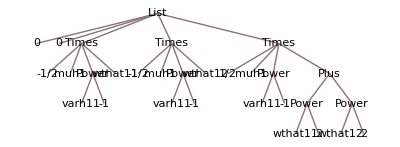

29

```mathematica
tf=TreeForm[eqs]
Length[Level[tf,Depth[tf]]]-1
```

## Eat

```mathematica
getNMoment3[idxs_]:=nMoments3[Sort[idxs]]
```

```mathematica
makeRepsEat[iHunter_,iPrey_]:=Module[
{muTEreps,nvarTEreps,x,y}
,
muTEreps=Table[
x=ToExpression["muTE"<>ToString[jSp]];
If[jSp==iPrey,
x->-nvar[[iHunter,iPrey]],
If[jSp==iHunter,
x->nvar[[iHunter,iPrey]],
x->0
]],{jSp,n}];

nvarTEreps={};
Do[
x=ToExpression["nvarTE"<>ToString[Min[jSp,kSp]]<>ToString[Max[jSp,kSp]]];

If[jSp==iPrey&&kSp==iPrey,
y=-2*getNMoment3[{iPrey,iPrey,iHunter}]+nvar[[iHunter,iPrey]];
AppendTo[nvarTEreps,x->y];
];

If[jSp==iHunter&&kSp==iHunter,
y=2*getNMoment3[{iHunter,iHunter,iPrey}]+nvar[[iHunter,iPrey]];
AppendTo[nvarTEreps,x->y];
];

If[(jSp==iHunter&&kSp==iPrey)||(jSp==iPrey&&kSp==iHunter),
y=-getNMoment3[{iHunter,iHunter,iPrey}]+getNMoment3[{iHunter,iPrey,iPrey}]-nvar[[iHunter,iPrey]];
AppendTo[nvarTEreps,x->y];
];

If[kSp==iPrey&&(jSp≠iHunter&&jSp≠iPrey),
y=-getNMoment3[{jSp,iPrey,iHunter}];
AppendTo[nvarTEreps,x->y]
];

If[jSp==iPrey&&(kSp≠iHunter&&kSp≠iPrey),
y=-getNMoment3[{kSp,iPrey,iHunter}];
AppendTo[nvarTEreps,x->y]
];

If[kSp==iHunter&&(jSp≠iHunter&&jSp≠iPrey),
y=getNMoment3[{jSp,iPrey,iHunter}];
AppendTo[nvarTEreps,x->y]
];

If[jSp==iHunter&&(kSp≠iHunter&&kSp≠iPrey),
y=getNMoment3[{kSp,iPrey,iHunter}];
AppendTo[nvarTEreps,x->y]
];

,{jSp,n},{kSp,jSp,n}];

Return[Simplify[Join[muTEreps,nvarTEreps]]];
]
```

```mathematica
eqs=Flatten[Simplify[{bhatTE,wthatTE,sig2TE}/.makeRepsEat[3,1]]]
```

{-√varh11 wthat11-muh1 (bhat1+muh1 (-1+1/(√varh11)) wthat11),0,1/(2 varh11^(3/2))(muh1^2 (-1+√varh11) wthat11 (2 √varh11+wthat11)-varh11 wthat11 (2 √varh11+wthat11)-bhat1 (2 muh1 varh11+2 varh11^2+muh1 √varh11 wthat11)+2 muh1 varh11 (sig2-2 √varh11 wthat11+varh11 wthat11)),-((bhat1 muh1 √varh11+(-muh1^2 (-1+√varh11)+varh11) wthat11) wthat12)/(2 varh11^(3/2)),1/(2 varh11^(3/2))(nvarTE22 varh11^(3/2)-2 muh1 sig2 varh11^(3/2)+muh1^2 varh11 wthat11-2 muh1 sig2 varh11 wthat11-muh1^2 varh11^(3/2) wthat11+varh11^2 wthat11+2 muh1^2 √varh11 wthat11^2-2 muh1^2 varh11 wthat11^2+2 varh11^(3/2) wthat11^2+muh1^2 wthat11^3-muh1^2 √varh11 wthat11^3+varh11 wthat11^3+muh1^2 wthat11 wthat12^2-muh1^2 √varh11 wthat11 wthat12^2+varh11 wthat11 wthat12^2+bhat1 muh1 √varh11 (varh11+2 √varh11 wthat11+wthat11^2+wthat12^2))}

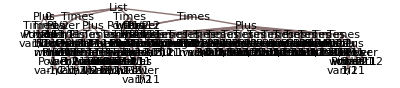

257

```mathematica
tf=TreeForm[eqs]
Length[Level[tf,Depth[tf]]]-1
```

## Birth

```mathematica
makeRepsBirth[iSp_]:=Module[
{muTEreps,nvarTEreps,x}
,
muTEreps=Table[
x=ToExpression["muTE"<>ToString[jSp]];
If[jSp==iSp,
x->mu[[iSp]],
x->0
],{jSp,n}];

nvarTEreps=Flatten[Table[
x=ToExpression["nvarTE"<>ToString[Min[jSp,kSp]]<>ToString[Max[jSp,kSp]]];
If[jSp==iSp&&kSp==iSp,
x->2*nvar[[iSp,iSp]]+mu[[iSp]],
If[jSp==iSp||kSp==iSp,
x->nvar[[jSp,kSp]],
x->0
]
]
,{jSp,n},{kSp,jSp,n}]];

Return[Join[muTEreps,nvarTEreps]];
]
```

# All reactions

```mathematica
noNodes={};
Do[
eqs=Flatten[Simplify[{bhatTE,wthatTE,sig2TE}/.makeRepsBirth[i]]];
tf=TreeForm[eqs];
AppendTo[noNodes,Length[Level[tf,Depth[tf]]]-1];
,{i,1,3}];

Do[
eqs=Flatten[Simplify[{bhatTE,wthatTE,sig2TE}/.makeRepsDeath[i]]];
tf=TreeForm[eqs];
AppendTo[noNodes,Length[Level[tf,Depth[tf]]]-1];
,{i,1,3}];

Do[
Do[
If[i≠j,
eqs=Flatten[Simplify[{bhatTE,wthatTE,sig2TE}/.makeRepsEat[i,j]]];
tf=TreeForm[eqs];
AppendTo[noNodes,Length[Level[tf,Depth[tf]]]-1];
];
,{j,1,3}];
,{i,1,3}];

noNodes
Total[noNodes]
Mean[noNodes]//N
```

{28,28,29,34,34,29,219,255,219,255,257,257}

1644

137.

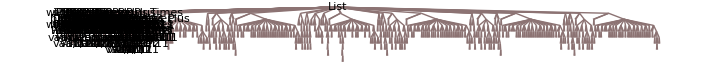

1644

```mathematica
eqs={};
Do[
AppendTo[eqs,Flatten[Simplify[{bhatTE,wthatTE,sig2TE}/.makeRepsBirth[i]]]];
,{i,1,3}];

Do[
AppendTo[eqs,Flatten[Simplify[{bhatTE,wthatTE,sig2TE}/.makeRepsDeath[i]]]];
,{i,1,3}];

Do[
Do[
If[i≠j,
AppendTo[eqs,Flatten[Simplify[{bhatTE,wthatTE,sig2TE}/.makeRepsEat[i,j]]]];
];
,{j,1,3}];
,{i,1,3}];

eqs=Flatten[eqs];
tf=TreeForm[eqs]
Length[Level[tf,Depth[tf]]]-1
```